# SRBench Competition Abstract

Nathan Haut
hautnath@msu.edu

Michigan State University

StackGP was used to generate the models in this submission. I used the Python based StackGP system, which is available in the StackGP.py file in the submission. This system is a stack-based implementation of GP that uses two stacks for symbolic regression problems, an operator stack and a variable/constant stack. The search is multi-objective, using Pareto-tournament selection to search for accurate, yet simple equations. Accuracy is determined using correlation, which has been shown to be more effective than RMSE [1]. For each problem I began by running a standard model search using default settings of StackGP with all of the variables in the data sets. From there I analyzed the populations to see which variables stood out as important. I then analyzed all of the input variables by doing a cross-correlation analysis, as well as a cross-modelling analysis. This revealed some relationships between some of the variables, so that some variables could be removed. These analyses are stored in the Mathematica notebooks “model1.nb”, “model2.nb”, and “model3.nb”. From there I ran some runs with StackGP using active learning to train models using the most informative points, selected iteratively. The code to train models is contained in the files “dataset_<num>_fitting.py”. Each of the steps are described in more detail below. Note that in the figures developed in Mathematica, since indexing begins at 1, there is an offset from the true input labels (example: x1 in Mathematica figure = x0 in original data).

1. Correlation Versus RMSE Loss Functions in Symbolic Regression Tasks. Haut, N.; Banzhaf, W.; and Punch, B. In Genetic Programming Theory and Practice XIX, pages 31-55. Springer Nature Singapore Singapore, 2023.

## Dataset 1

Initially, I plotted each of the input variables against the response to see if any obvious trends arise. The results are here, and don’t seem to show any obvious trends.

We do see though that most of the input variables are sampled from a bimodal distribution, while the response is a normal distribution.

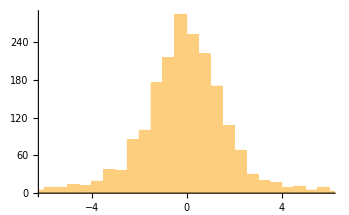
```mathematica
-Graphics--Graphics-
```

An initial run showed that 3 of the variables dominated. These correspond to variables x0, x1, and x6 from the initial set. We narrow the focus to these variables in the final model development.

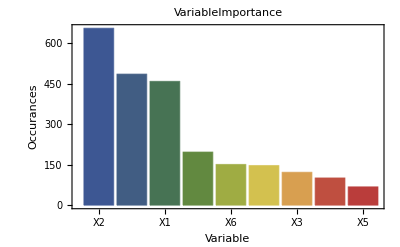

From the cross-modelling analysis we see that variable 3 appears to be highly correlated to variable 0, likely indicating it is a noisy version of variable 0. Variable 2 was found to have a high correlation to x0+x1, indicating that either x0 and x1 are noisy versions of x2, or x2 is composed of x0 and x1. Since x1 and x0 appeared more frequently in the search, it is assumed that those are informative and x2 is a noisy version of x0+x1. Variable 4 was found to have a high correlation to variable 1, which likely indicates it is a noisy version of 1. Variable 5 was found to have a high correlation to the equation 1/(π+x6)-x1. Variable 6 did not appear to have strong relationships with any other variables. Variable 7 had a high correlation with variable 0. Variable 8 appeared to be strongly correlated to x1. 

I then ran many rounds of modelling using active learning to select one point each iteration to add to the training set, until around 10% of the data was being used. The code used to generate the model is contained in “dataset_1_fitting.py”. The model discovered does perform poorly though with an R^2 value of only around 0.4. This could indicate that the dataset is very noisy, the needed operators weren’t included in the search space, or the model discovered was a local optima and more time was needed in the search.

## Dataset 2

The same steps were repeated with dataset 2. Again, no obvious relationships were observed when plotting all the input variables against the response.

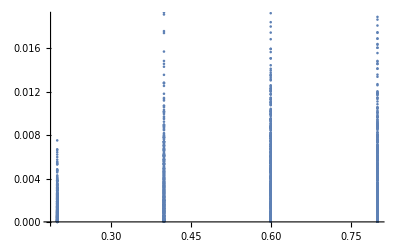
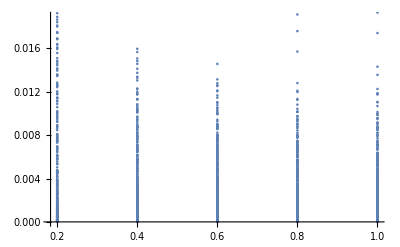
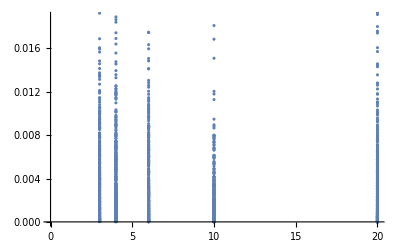
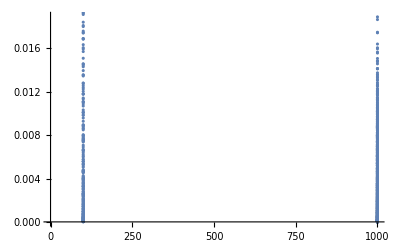
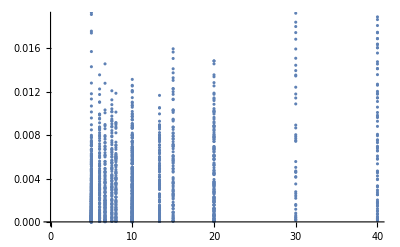
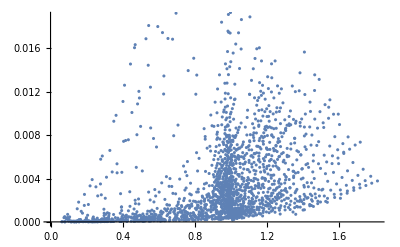
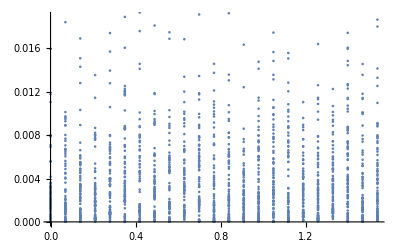

The input variables are distributed a bit differently though this time. We can see that many of them have discrete values.

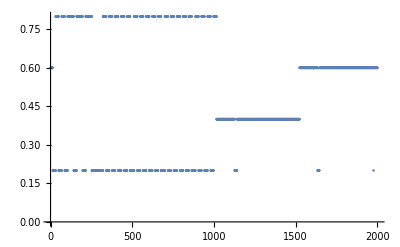
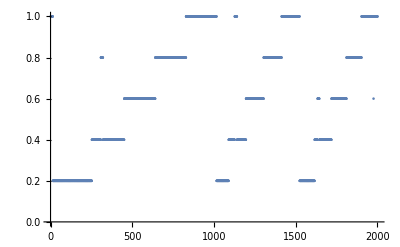
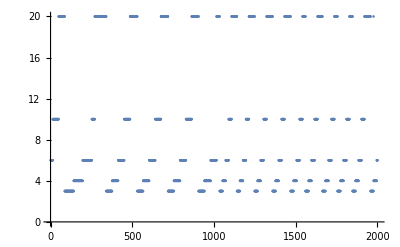
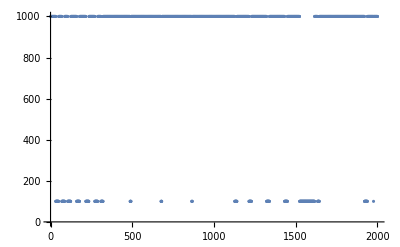
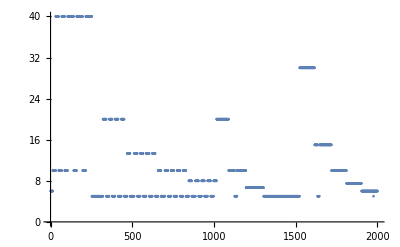
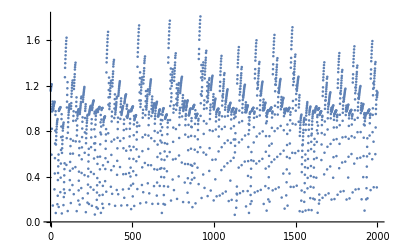
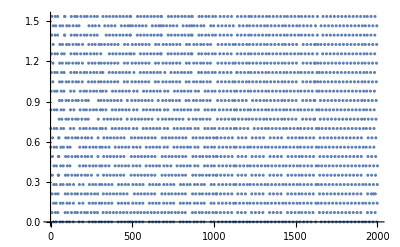

From the initial run, we see again that 4 variables appeared more frequently. Without removing variables a relatively high fitness was achieved, so all were left in the search space.

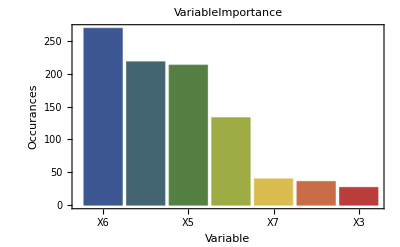

The code to develop the model for this dataset is in “dataset_2_fitting.py”. A relatively small function was found with a R^2 value of around 0.95.

## Dataset 3

The same steps were also repeated with dataset 3. This dataset was larger with 16 input variables. Again, no trends were obvious by plotting the inputs against the response.

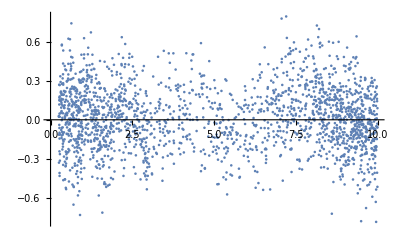
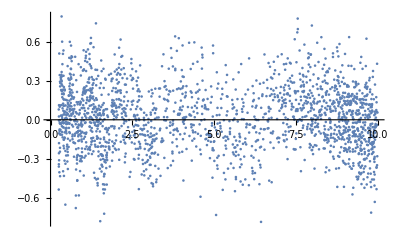
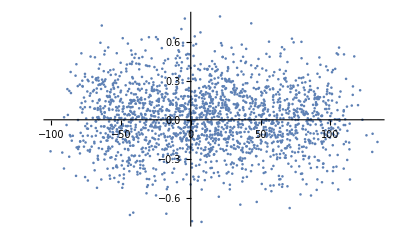
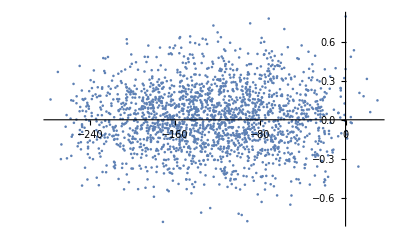
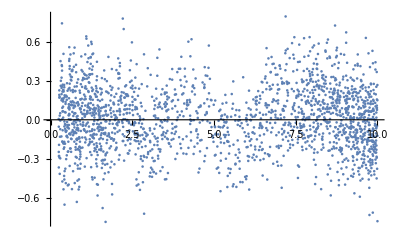
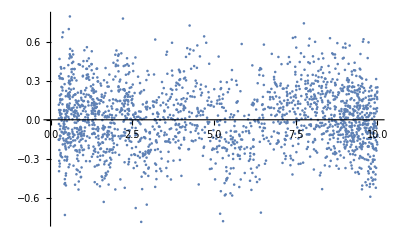
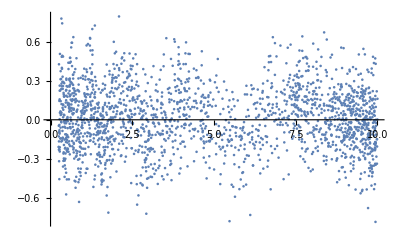
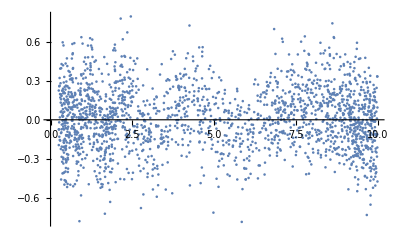

We can see that most of the distributions were either bimodal or normal.

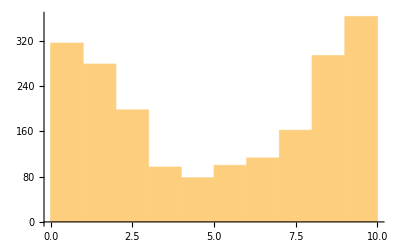
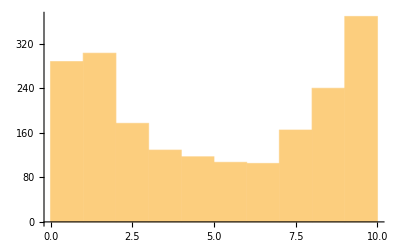
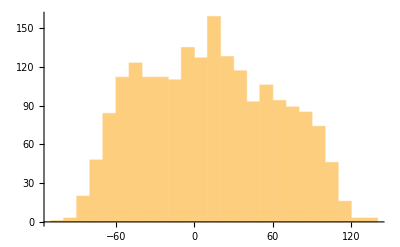
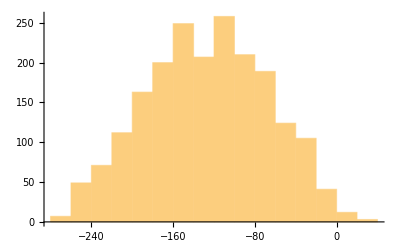
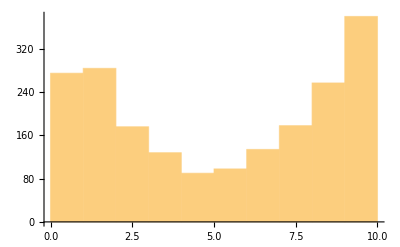
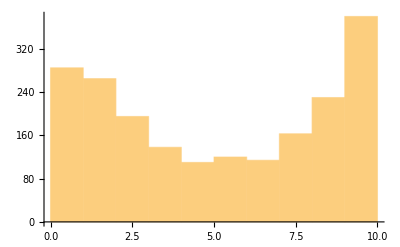
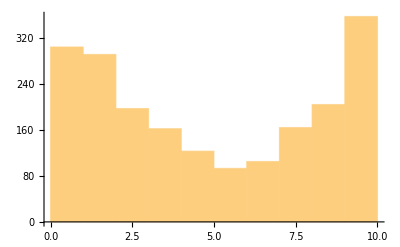
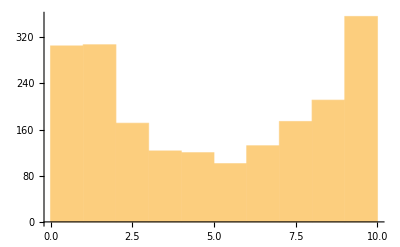

The response is a normal distribution.

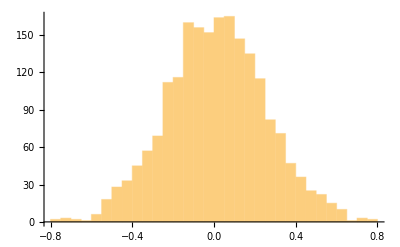

We can see that one variable dominated over the rest in terms of frequence of appearance during initial runs. This corresponds to x10 in the dataset. Initially I tried restricting the search using the top 3 variables, x10, x1, and x11, but results were not great, so I expanded to using the full set. Eventually the best model I was able to find used 7 of the 16 variables, x0, x1, x4, x5, x6, x7, and x11.

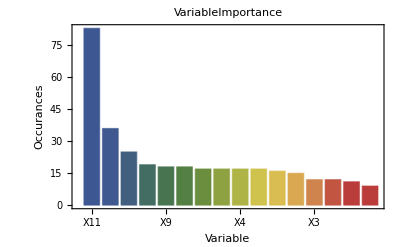

The cross-modelling analysis revealed that there was a strong relationship between x1 and x8. The variable x2 also seemed to have a high correlation to the function x11-x4. The variable x3 had a high correlation to the function e^(x11^0.25)+x15+Sqrt[x1]+x6. Variable x4 had a high correlation to x11-x2, but that correlation was weaker than the relationship between x2 and x11-x4. X5 had a high correlation to x15. x7 and x14 also had a high correlation. X9 had a somewhat high correlation to the equation x1+x6-x11. X10 had a high correlation to the function x0^2+x6+x12. X11 had a strong correlation to the equation x2+x4^2-x9. x12 had a high correlation to the function x10-Sqrt[x0]. x13 had a high correlation to the equation x3+x10+x11^2. These strong relationships between all of the variables could be part of what made this problem challenging. 

Ultimately, a function with an R^2 of around 0.85 was found between the inputs and the response. This equation was -(5.34*10**(-4))+0.12*sin(log(x11**10))+0.12*(sin(log(x4**10))+6.32*(0.17*sin(log(x0**10))+0.17*sin(log(x1**10))+0.17*sin(log(x5**10)))+sin(log(x6**10))+sin(log(x7**10))). The structure was very interesting since it is a bunch of terms added together that each have the form sin(log(variable**10)). Since the form of the equation was very structured I assume I arrived at something close to the synthetic generating function. For a long time I was stuck on a simpler equation that had some similarities, but didn’t have a great accuracy score: 0.14149309132864*sin(sin(10.0331602811267*log(x10))) + 0.14149309132864*atan(asin(sin(10.0331602811267*log(x1)))) + 0.01372340750873.